```mathematica
CodonSequence=Import["C:\Up\Proteins\Ribosomal (All)\aspS.txt"];FreeEnergySignal=Import["C:\Up\Presentation Data\Mathematica Animations\aspS Data\FreeEnergySignal","CSV"][[1]];DisplacementValues=Import["C:\Up\Presentation Data\Mathematica Animations\aspS Data\DisplacementValues","CSV"][[1]];DisplacementDifferences=Import["C:\Up\Presentation Data\Mathematica Animations\aspS Data\DisplacementDifferences","CSV"][[1]];ForceDifferences=Differences[DisplacementDifferences];LeaderSequence="auuccuccacuag";
```

```mathematica
NucleotideSequence[n_]:=StringTake[CodonSequence,{3n-2,3n+17}];
```

```mathematica
BackgroundPlot[n_]:=GraphicsGroup[{
{Opacity[0.35,LightGray],Rectangle[{-1,-1},{11,6}]},{LightBlue,Rectangle[{-0.5,-0.5},{2.5,2.5}],Inset[ListPlot[Take[FreeEnergySignal,n],PlotRange->{{0,30},{1,-11}},Joined->True,Axes->True,Ticks->None,AspectRatio->1,PlotStyle->Thick,Filling->Axis],{-0.5,2.25},{0,0},{3,3}]},{EdgeForm[Brown],FaceForm[LightBrown],Rectangle[{1.27,4},{6.55,5.5}]},{Text[Style[NucleotideSequence[n],Black,FontFamily->"Consolas",FontSize->18],{5,4.5}]},
{Text[Style[LeaderSequence,Black,FontFamily->"Consolas",FontSize->18],{3.95,5.25}]},{LightCyan,Rectangle[{3.5,-0.5},{6.5,2.5}],Inset[ListPlot[Take[ForceDifferences,n],PlotRange->{{0,30},{-2.5,2.5}},Joined->True,Axes->True,Ticks->None,AspectRatio->1,PlotStyle->Thick,Filling->Axis],{3.5,1},{0,0},{3,3}]},{LightGreen,Rectangle[{7.5,-0.5},{10.5,2.5}],Inset[ListPlot[Take[DisplacementValues,n],PlotRange->{{0,30},{-0.5,2.5}},Joined->True,Axes->True,Ticks->None,AspectRatio->1,PlotStyle->Thick,Filling->Axis],{7.5,0},{0,0},{3,3}]}
}];
```

```mathematica
ReadingFrame[n_]:=GraphicsGroup[{
{Black,Line[{
{7.05+DisplacementValues[[n]]*0.208,4.1},
{7.05+DisplacementValues[[n]]*0.208,3.85},
{8.22+DisplacementValues[[n]]*0.208,3.85},
{8.22+DisplacementValues[[n]]*0.208,4.1}
}]},
{Black,Line[{
{7.05+DisplacementValues[[n]]*0.208,4.75},
{7.05+DisplacementValues[[n]]*0.208,5},
{8.22+DisplacementValues[[n]]*0.208,5},
{8.22+DisplacementValues[[n]]*0.208,4.75}
}]},
{Black,Arrowheads[0.03],
Arrow[{{2.5,1.5},{3.5,1.5}}],
Arrow[{{6.5,0.5},{7.5,0.5}}],
Arrow[{{3.91,4},{3.91,3.25},{1,3.25},{1,2.5}}],
Arrow[{{9,2.5},{9,3.25},{7.85,3.25},{7.85,3.85}}]
}
}];
```

```mathematica
List1=Table[Graphics[{BackgroundPlot[n],ReadingFrame[n]}],{n,1,30}];
```

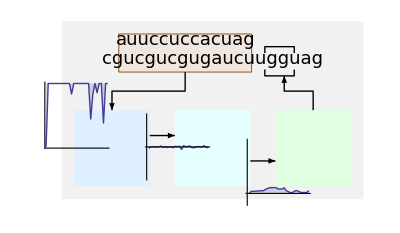

```mathematica
List1[[30]]
```

```mathematica
Export["aspS-animation.gif",List1];
```